6.)

```mathematica
sizesAndTimes = 
Table[
{
n,
Timing[Det[RandomInteger[{1,10},{n,n}]]][[1]]
},
{n,50,500,50}
]
```

{{50,0.042135},{100,0.04696},{150,0.094159},{200,0.192966},{250,0.341134},{300,0.616417},{350,1.01071},{400,1.54594},{450,2.09541},{500,2.90159}}

a.)

```mathematica
cubic = Fit[sizesAndTimes,{1,x,x^2,x^3},x]
```

0.0929509-0.00111952 x+4.16933×10^-6 x^2+1.85749×10^-8 x^3

b.)

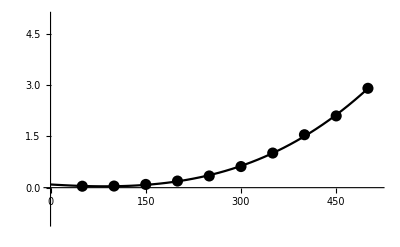

```mathematica
Plot[
cubic,
{x,0,500},
PlotStyle->Black,
PlotRange->{{0,515},{-1,5}},
Epilog->{
Black,PointSize[0.02],Point[sizesAndTimes]
}
]
```

c.)

```mathematica
x = 5000;
0.09295086666666698-0.0011195181507381478 x+4.1693312354312126*^-6 x^2+1.857485470085473*^-8 x^3
```

2420.59

The cubic function predicts 2420.59 seconds, which = 40.34 minutes

```mathematica
Timing[Det[RandomInteger[{1,10},{5000,5000}]]][[1]]
```

Wouldn’t this take 40 minutes?

d.)

```mathematica
Clear[x];
Solve[0.09295086666666698-0.0011195181507381478 x+4.1693312354312126*^-6 x^2+1.857485470085473*^-8 x^3== 31 10^6,x]
```

{{x→-59383.2-102725. ⅈ},{x→-59383.2+102725. ⅈ},{x→118542.}}

You would need an 118542 x 118542 matrix for it to take one year to compute

e.)

Idk yet